```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
loadTimeSeriesResampledShiftneg1=TimeSeriesShift[loadTimeSeriesResampled,{-1,"Hour"}]
```

TimeSeries[…]

```mathematica
DateListPlot[TimeSeriesWindow[loadTimeSeriesResampled,DateObject[{2019,1,1}],DateObject[{2019,1,2}]]]
```

DateListPlot::ldata: TimeSeriesWindow[«1»] is not a valid dataset or list of datasets.

DateListPlot[TimeSeriesWindow[TimeSeries[…],Day: Tue 1 Jan 2019,Day: Wed 2 Jan 2019]]

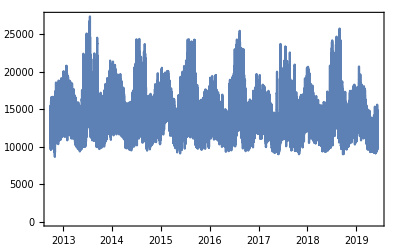

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
DateListPlot[loadTimeSeriesResampledShiftneg1]
```

-Graphics-

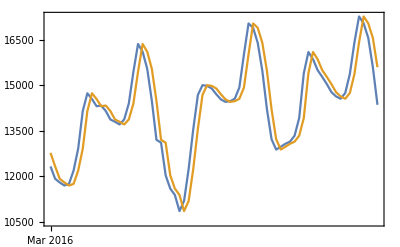

```mathematica
DateListPlot[{TimeSeriesWindow[loadTimeSeriesResampledShiftneg1,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}],TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}]}]
```

```mathematica
loadTimeSeriesResampledShiftneg1=TimeSeriesShift[loadTimeSeriesResampled,{-1,"Hour"}]
```

```mathematica
loadTemportalDataShifttoNeg30=TemporalData[{
TimeSeriesShift[loadTimeSeriesResampled,{-1,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-2,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-3,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-4,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-5,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-6,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-7,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-8,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-9,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-10,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-11,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-12,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-13,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-14,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-15,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-16,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-17,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-18,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-19,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-20,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-21,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-22,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-23,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-24,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-25,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-26,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-27,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-28,"Hour"}],TimeSeriesShift[loadTimeSeriesResampled,{-29,"Hour"}],
TimeSeriesShift[loadTimeSeriesResampled,{-30,"Hour"}]
}]
```

TemporalData[<<30>>]

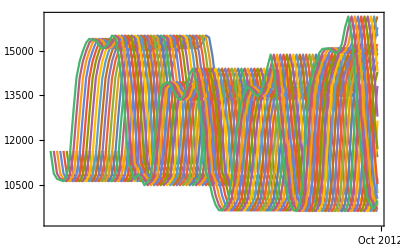

```mathematica
DateListPlot[TimeSeriesWindow[loadTemportalDataShifttoNeg30,{DateObject[{2012,9,26}],DateObject[{2012,9,30}]}]]
```